```mathematica
ContourPlot[{ x/Tan[Pi/4+Pi/36]< y,x/Tan[Pi/4-Pi/36]>y},{x,-5,5},{y,-5,5}]
```

ContourPlot::invefunc: x/Tan[π/4+π/36]<y must be a function f or an equality of the form f == g.

General::stop: Further output of ContourPlot::invefunc will be suppressed during this calculation.

ContourPlot[{x/Tan[π/4+π/36]<y,x/Tan[π/4-π/36]>y},{x,-5,5},{y,-5,5}]

```mathematica
ContourPlot3D[{ x/Tan[Pi/4+Pi/36]==z ,x/Tan[Pi/4-Pi/36] ==z, y/Tan[Pi/6+Pi/18]==z,y/Tan[Pi/6-Pi/18]},{x,-5,5},{y,-5,5},{z,-5,5}]
```

```mathematica
-Graphics3D-
RegionPlot3D[ x/Tan[Pi/4+Pi/36]<z && x/Tan[Pi/4-Pi/36]>z && y/Tan[Pi/6+Pi/18 ]<z &&y/Tan[Pi/6-Pi/18]> z, {x,-5,5},{y,-5,5},{z,-5,5}]
```

-Graphics3D-

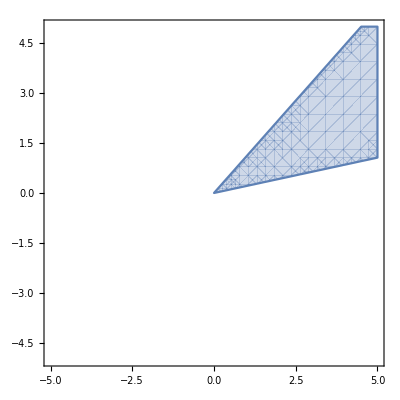

```mathematica
RegionPlot[x/Tan[Pi/3+Pi/10] < y  && x/Tan[Pi/3-Pi/10] > y,{x,-5,5},{y,-5,5}]
```

```mathematica
RegionPlot3D[ x/Tan[Pi/4-Pi/36]<z < x/Tan[Pi/4+Pi/36] && y/Tan[Pi/4-Pi/36 ]<z <y/Tan[Pi/4+Pi/36], {x,-5,5},{y,-5,5},{z,-5,5},PlotPoints -> 50]
```

-Graphics3D-

```mathematica
Manipulate[RegionPlot3D[x/Tan[θ-ϵ]<z < x/Tan[θ+ϵ],{x,-5,5},{y,-5,5},{z,-5,5},PlotRange ->All],{θ,0.001,Pi/2.000001},{ϵ,Pi/36,Pi/4}]
```

```mathematica
RegionPlot3D[ x/Tan[Pi/4-Pi/36]>z > x/Tan[Pi/4+Pi/36],{x,-5,5},{y,-5,5},{z,-5,5}]
```

-Graphics3D-

```mathematica
RegionPlot3d[ k/Tan[Pi/4+Pi/36]<z <k/Tan[Pi/4-Pi/3],{k,-5,5},{y,-5,5},{z,-5,5}]
```

RegionPlot3d[k Tan[(2 π)/9]<z<k/(-2+√3),{k,-5,5},{y,-5,5},{z,-5,5}]